```mathematica
A = Expand[(x^2-(1/2))^2]
```

1/4-x^2+x^4

```mathematica
B = A * Exp[-x^2]
```

ⅇ^(-x^2) (1/4-x^2+x^4)

```mathematica
Integrate[B,{x,-Infinity, Infinity}]
```

(√π)/2

```mathematica
Integrate[Exp[-x^2]/4, {x,-Infinity, Infinity}]
```

(√π)/4

Root0.443Root[1-#1-#1^2-2 #1^3-3 #1^4-3 #1^5-2 #1^6-2 #1^7-2 #1^8+4 #1^9+6 #1^10+5 #1^11+3 #1^12&,1]0.4431134627262045

```mathematica
Integrate[(-x^2)*Exp[-x^2], {x,-Infinity, Infinity}]
```

-(√π)/2

```mathematica
Integrate[(x^4)*Exp[-x^2], {x,-Infinity, Infinity}]
```

(3 √π)/4

```mathematica
(Sqrt[Pi]/4)- (Sqrt[Pi]/2) + (3*Sqrt[Pi]/4)
```

(√π)/2

```mathematica
a20 = Integrate[(x^2*Exp[-x^2]),{x,-Infinity,Infinity}]
```

(√π)/2

```mathematica
solucion = 1/(2^3*Pi^(1/2))
```

1/(8 √π)

```mathematica
solucion = solucion * a20
```

1/16

```mathematica
Integrate[2*x^3*Exp[-x^2],{x,-Infinity, Infinity}]
```

0

```mathematica
Integrate[(x^2-(1/2))^2*Exp[-x^2],{x,-Infinity,Infinity}]
```

(√π)/2

```mathematica
Plot[HermiteH[0,x],HermiteH[1,x], HermiteH[2,x]]
```

Plot::nonopt: Options expected (instead of HermiteH[2,x]) beyond position 2 in Plot[HermiteH[0,x],HermiteH[1,x],HermiteH[2,x]]. An option must be a rule or a list of rules.

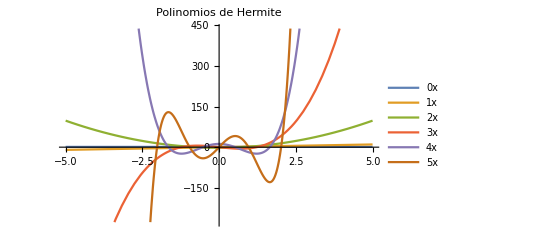

```mathematica
graf1 = Plot[{HermiteH[0,x],HermiteH[1,x],HermiteH[2,x], HermiteH[3,x], HermiteH[4,x],HermiteH[5,x]},{x,-5,5}, PlotLegends->"Expressions", PlotLabel->"Polinomios de Hermite"]
```

```mathematica
Export["Plot_Hermite.eps", graf1]
```

Plot_Hermite.eps

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["Plot_Hermite.eps"]]]
```

```mathematica
Plot[HermiteH[n,x],{n,10},{x,-10,10},PlotLabels->"Expressions"]
```

Plot::nonopt: Options expected (instead of {x,-10,10}) beyond position 2 in Plot[HermiteH[n,x],{n,10},{x,-10,10},PlotLabels→Expressions]. An option must be a rule or a list of rules.

Plot[HermiteH[n,x],{n,10},{x,-10,10},PlotLabels→Expressions]